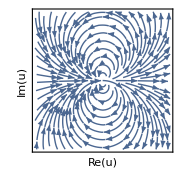

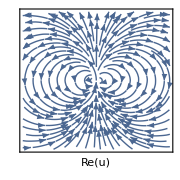

```mathematica
NstreamPoints=50;
StreamHeat=ComplexStreamPlot[u^2,{u,-1-I,1+I},ImageSize->Small,StreamColorFunction->Blue,FrameLabel->{{"Im(u)",},{"Re(u)",}},StreamScale->Large,RotateLabel->False,GridLines->Automatic,FrameTicks->None]
StreamNLS=ComplexStreamPlot[-I u^2,{u,-1-I,1+I},ImageSize->Small,StreamColorFunction->Blue,StreamScale->Large,FrameTicks->None,RotateLabel->False,GridLines->Automatic,FrameLabel->{{,"Im(u)"},{"Re(u)",}}]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\JonoS\Dropbox\etc\NLS\Real_initial_data\Final_Code\Mathematica

```mathematica
imRes=400;
```

```mathematica
Export["Stream_Heat.png",StreamHeat,ImageResolution->imRes]
```

Stream_Heat.png

```mathematica
Export["Stream_NLS.png",StreamNLS,ImageResolution->imRes]
```

Stream_NLS.png